1/4 M (1+M) N (1+N)

{{x→ConditionalExpression[-1/2+1/2 √((32000000+y+y^2)/(y (1+y))), y>0]}}

{{x→Root52.7Root[-8000000+#1^2+2 #1^3+#1^4&,2]52.68530929444888}}

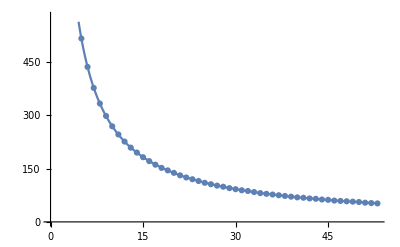

2772

```mathematica
formula=Sum[(M-m+1)*(N-n+1),{m,1,M},{n,1,N}]//FullSimplify

num[M_,N_]:=1/4 M (1+M) N (1+N)
Solve[num[x,y]==2*10^6,x,PositiveReals]
Solve[num[x,x]==2*10^6,x,PositiveReals]

f[y_]:=-1/2+1/2 √((32000000+y+y^2)/(y (1+y)))
func[y_]:=f[y]//Round
ntnm[x_]:={x,func[x],num[x,func[x]],Abs[num[x,func[x]]-2*10^6]}
data=Table[ntnm[n],{n,1,53}];
Show[{ListPlot@(#[[1;;2]]&/@data),Plot[f[x],{x,1,53}]}]
res=MinimalBy[data,Last];
Times@@res[[1,1;;2]]
```